# Pregunta 2 Tarea 4

```mathematica
gravityConstant=ℊ;
𝓇=leyMovimiento;
𝓋=leyVelocidad;
```

WolframAlphaQueryParseResults

9.8 m/s^2

```mathematica
L=2;(*m*)
ω=1.3;(*rad/s*)
ℊ=QuantityMagnitude[Quantity[9.8`3., ("Meters")/("Seconds")^2]];
```

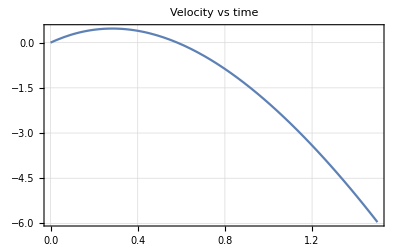

```mathematica
Plot[𝓋[t,L,ω],{t,0,1.5},
Frame->True,PlotRange->All,GridLines->Automatic,
PlotLabel->Style["Velocity vs time",16]
]
```

```mathematica
tmax=t/.FindRoot[𝓋[t,L,ω],{t,1}][[1]]
```

0.582214

### Posicion más distante:

```mathematica
Quantity[𝓇[tmax,L,ω],"Meters"]
```

2.18153 m

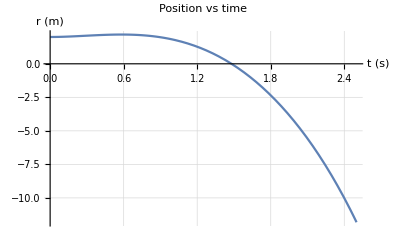

```mathematica
p1=Plot[𝓇[t,L,ω],{t,0,2.5},PlotRange->All,GridLines->Automatic,
PlotLabel->Style["Position vs time",16],AxesLabel->{Style["t (s)",12],Style["r (m)",12]}
]
```

### Punto inferior del plano

```mathematica
tr0=Quantity[t/.FindRoot[𝓇[t,L,ω],{t,2}][[1]],"Seconds"]
```

1.47973 s

Punto en el que la pelota despeja del plano inclinado es cuando θ = π/2 -> t = π/2 ω

```mathematica
tplano=Quantity[π/(2ω),"Seconds"]
```

1.2083 s

```mathematica
l1=Graphics[{Thick,Dashed,Line[{{𝓇[π/(2ω),L,ω],-13},{𝓇[π/(2ω),L,ω],3}}]}];
```

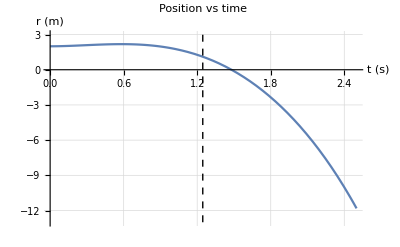

```mathematica
Show[p1,l1]
```

#### Del gráfico podemos observar que segundo el modelo planteado la particula deja el plano inclinado antes de llegar al origen o centro del plano . Segun el modelo la particula deja el plano en el segundo 1.2083 s pero llega al origen en 1.47973 s . El resultado que tiene sentido solo es el primero, el tiempo en que llega a una máxima distancia .

# Classical Mechanics

### Small Coupled Oscillations

Generalized coordinates

T=1/2∑_jk ((∂^2 T)/(∂(q̇)_j∂(q̇)_k))_(q=0)(q̇)_j(q̇)_k=1/2∑_jk T_jk(q̇)_j(q̇)_k

U=1/2∑_jk ((∂^2 U)/(∂q_j∂q_k))_(q=0)q_j q_k=1/2∑_jk V_jk q_j q_k

The equations of motion

∑_j (V_jk q_j+T_jk(q^(..))_j)=0

Oscillation modes

q_j(t)=a_j ⅇ^(i(w t -δ))

Eigenvalue equation

∑_j (V_jk+ω^2 T_jk)a_j=0

(V-ω^2 T)a=0

General Solution

Q_j(t)=Re(∑_r a_jr ⅇ^(ⅈ(ω_r t-δ_r)))=∑_r a_jr cos(ω_r r-δ_r)

### Example

Consider the following system:

-Graphics-

Write the energy expressions

```mathematica
q={x[1][t],x[2][t]};
```

```mathematica
T=1/2 m (x[1]'[t])^2+1/2 m (x[2]'[t])^2;
```

```mathematica
V=1/2 k2 (x[1][t])^2+1/2 k2 (x[2][t])^2+1/2 k1(x[2][t]-x[1][t])^2;
```

Solution of the eigenvalue problem

```mathematica
sol=solveSmallCoupledOscillations[T,V,q,t]
```

Potential energy matrix  {{k1+k2,-k1},{-k1,k1+k2}}

Kinetic energy matrix  {{m,0},{0,m}}

{{k2/m,(2 k1+k2)/m},{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}}

Generate rules to replace solutions

```mathematica
values={k1->1,k2->1,m->1,ϕ1->0,ϕ2->0}
```

{k1→1,k2→1,m→1,ϕ1→0,ϕ2→0}

```mathematica
frequencyRules=Thread[{ω1,ω2}->√sol[[1]]]
```

{ω1→√(k2/m),ω2→√((2 k1+k2)/m)}

```mathematica
motionRules=Thread[{x1[t],x2[t]}->Transpose[sol[[2]]].{c1 Cos[ω1 t+ϕ1],c2 Cos[ω2 t +ϕ2]}]
```

{x1[t]→(c1 Cos[ϕ1+t ω1])/(√2)-(c2 Cos[ϕ2+t ω2])/(√2),x2[t]→(c1 Cos[ϕ1+t ω1])/(√2)+(c2 Cos[ϕ2+t ω2])/(√2)}

```mathematica
allRules=Join[motionRules,frequencyRules,values]
```

{x1[t]→(c1 Cos[ϕ1+t ω1])/(√2)-(c2 Cos[ϕ2+t ω2])/(√2),x2[t]→(c1 Cos[ϕ1+t ω1])/(√2)+(c2 Cos[ϕ2+t ω2])/(√2),ω1→√(k2/m),ω2→√((2 k1+k2)/m),k1→1,k2→1,m→1,ϕ1→0,ϕ2→0}

Plotting the oscillations in time and phase space

```mathematica
plotOscillations[cRules_]:=
Module[{plot1,plot2},
plot1=Plot[Evaluate[{x1[t],x2[t]}//.allRules//.cRules],{t,0,20},
PlotStyle->{{Thickness[0.01]},{Thickness[0.005]}}];
plot2=ParametricPlot[Evaluate[{x1[t],x2[t]}//.allRules//.cRules],{t,0,20},AxesLabel->{x1,x2}];
Show[GraphicsRow[{plot1,plot2}]]]
```

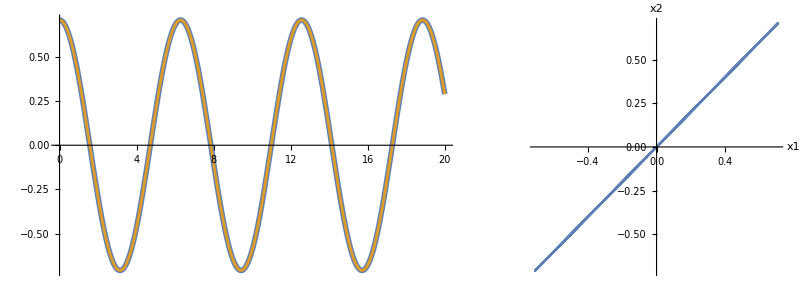

```mathematica
plotOscillations[{c1->1,c2->0}]
```

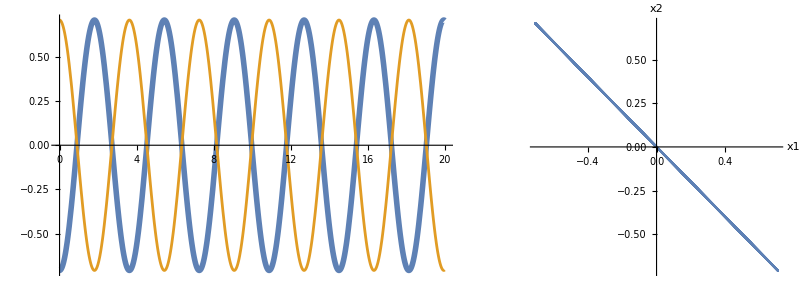

```mathematica
plotOscillations[{c1->0,c2->1}]
```

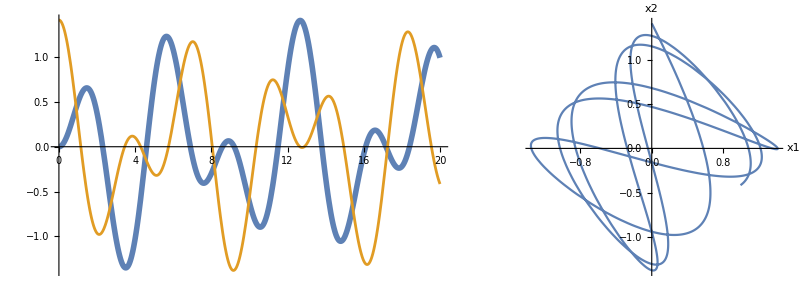

```mathematica
plotOscillations[{c1->1,c2->1}]
```

```mathematica
Evaluate[{x1[t],x2[t]}//.allRules]
```

{(c1 Cos[t])/(√2)-(c2 Cos[√3 t])/(√2),(c1 Cos[t])/(√2)+(c2 Cos[√3 t])/(√2)}

# Pregunta 3 Tarea 5

#### Cargamos el paquete: Al correr esta sección cambiar los “...” en la dirección “.../WorkSpaces/CompPhys2/MathMethods/ODE.m”.

```mathematica
Import["C:/Users/erik_/Documents/erik documents/PUCP/Maestria-Fisica/Ciclo-2/Fisica_Computacional/WorkSpaces/CompPhys2/MathMethods/ODE.m"]
```

ODE definitions loaded.

```mathematica
f[t_,{x_,y_}]:={y,(1-x^2)y-x}
```

```mathematica
ODESol=RK4NDSolve[f,{0.5,0},{0,50,2000}];
```

```mathematica
times=ODESol[[1]];
xSol=ODESol[[2]][[1]];
ySol=ODESol[[2]][[2]];
```

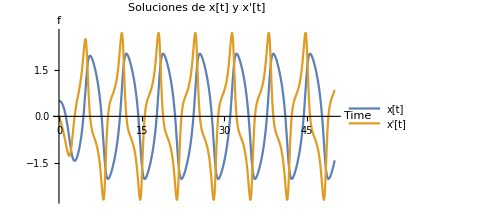

```mathematica
ListLinePlot[{xSol,ySol},DataRange->{0,50},ImageSize->Medium,PlotLabel->Style["Soluciones de x[t] y x'[t]",15],PlotLegends->{"x[t]","x'[t]"},AxesLabel->{Style["Time",12],Style["f",12]}]
```

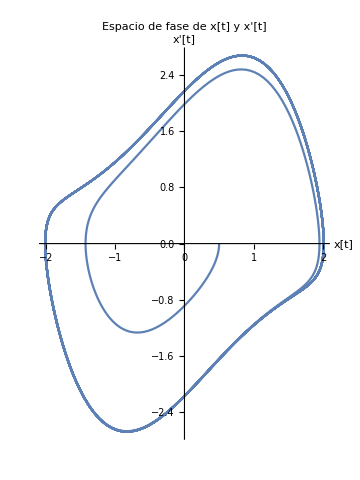

```mathematica
ListLinePlot[Transpose[{xSol,ySol}],AspectRatio->Automatic,ImageSize->Medium,PlotLabel->Style["Espacio de fase de x[t] y x'[t]",15],AxesLabel->{Style["x[t]",13],Style["x'[t]",13]}]
```

#### Interpolacion:

```mathematica
interp=Interpolation[Transpose[{times,xSol}]]
```

InterpolatingFunction[…]

#### Buscamos las raices cada t = 1.

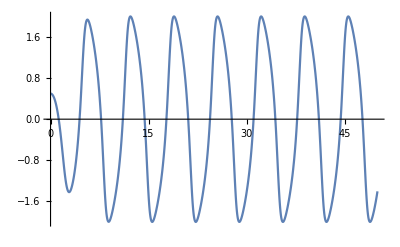

```mathematica
Plot[interp[x],{x,0,50}]
```

```mathematica
startingPoints=Table[i,{i,2,45}];(*puntos para iniciar busqueda de raices en todo el espacio desde 2 hasta 45*)
```

```mathematica
rootsRules=FindRoot[interp[x],{x,#}]&/@startingPoints(*Calculamos las raices*)
```

{{x→1.24823},{x→4.44041},{x→4.44041},{x→4.44041},{x→11.0618},{x→7.73163},{x→7.73163},{x→21.0567},{x→11.0618},{x→11.0618},{x→11.0618},{x→14.3934},{x→14.3934},{x→14.3934},{x→21.0567},{x→17.725},{x→17.725},{x→34.3832},{x→21.0567},{x→21.0567},{x→21.0567},{x→24.3883},{x→24.3883},{x→24.3883},{x→31.0516},{x→27.7199},{x→27.7199},{x→34.3832},{x→31.0516},{x→31.0516},{x→31.0516},{x→34.3832},{x→34.3832},{x→34.3832},{x→41.0465},{x→37.7149},{x→37.7149},{x→47.7098},{x→41.0465},{x→41.0465},{x→37.7149},{x→44.3782},{x→44.3782},{x→44.3782}}

```mathematica
roots=Sort[(x/.#)&/@rootsRules](*extraemos las raices*)
```

{1.24823,4.44041,4.44041,4.44041,7.73163,7.73163,11.0618,11.0618,11.0618,11.0618,14.3934,14.3934,14.3934,17.725,17.725,21.0567,21.0567,21.0567,21.0567,21.0567,24.3883,24.3883,24.3883,27.7199,27.7199,31.0516,31.0516,31.0516,31.0516,34.3832,34.3832,34.3832,34.3832,34.3832,37.7149,37.7149,37.7149,41.0465,41.0465,41.0465,44.3782,44.3782,44.3782,47.7098}

```mathematica
periodos=roots[[2;;]]-roots[[;;-2]](*El periodo es el espacio entre raices, restamos raices consecutivas*)
```

{3.19218,0.,0.,3.29122,0.,3.33014,0.,0.,0.,3.3316,0.,0.,3.33164,0.,3.33164,0.,0.,0.,0.,3.33164,0.,0.,3.33164,3.55271×10^-15,3.33164,0.,0.,0.,3.33164,0.,0.,0.,0.,3.33164,0.,0.,3.33164,0.,0.,3.33164,0.,0.,3.33164}

#### Periodo:

```mathematica
periodo=2*Cases[periodos,x_/;x>10^-10][[-1]](*Algunas raices se contraron multiples veces, por tanto, al restar resultaron en 0 o numeros cercanos a 0, ponemos una tolerancia de error de 10^-10, el periodo mas estable es el ultimo valor *2*)
```

6.66329

#### Podemos observar que apartir de t = 17.725 el sistema tiene un periodo estable . Integramos la EDO desde 0 hasta 17.725 + 5 * T

Extraemos las raices en donde empieza el periodo estable

```mathematica
positions=(#<10^-6)&/@Abs[periodo/2-periodos](*obtenemos la posicion en donde estan los valores nulos de periodos - periodo*)
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,True,False,True,False,False,False,True,False,False,False,False,True,False,False,True,False,False,True,False,False,True}

```mathematica
positionRoot=Position[positions,True][[1]][[1]](*Extraemos el primer indice*)
```

15

En este punto inicia el periodo estable:

```mathematica
initTime=roots[[positionRoot]](*En este tiempo (raiz) inicia el periodo estable*)
```

17.725

Definimos una funcion que nos resulve la EDO con RK4NDSolve con n puntos, un punto inicial dado y k periodos y nos retorna la funcion interpolada con tales parametros especificados, esto para poder luego hacer el grafico del espectro de energia.

```mathematica
SignalConstructorEDO[initialTime_,period_,numperiods_,points_]:=
Module[{ODEsol,timesList,xSolList,ySolList,var1,initTimeIndex,sample,interpolatedFunction},
(* integrmos de 0 hasta TiempoInicial + NumberOfPeriods * Period con "points" puntos. Con esto nos aseguramos que x habra llegado a la etapa de periodo estable*)
ODEsol=RK4NDSolve[f,{0.5,0},{0,initialTime+numperiods*period,points}];
timesList=ODEsol[[1]];
xSolList=ODEsol[[2]][[1]];
ySolList=ODEsol[[2]][[2]];
(*Dado que el integrador integra desde 0 debemos extraer solo los valores de x apartir de "initialTime" o el valor más cercano. Encontramos el tiempo inicial de periodo estable restando este valor a la lista de tiempos obtenidos de RK4NDSolve*)
var1=Min[Abs[timesList-initialTime]];
initTimeIndex=Position[Abs[timesList-initialTime],var1][[1]][[1]];(*posicion del array en donde inicial el periodo estable*)

sample=Transpose[{timesList[[;;(Length[timesList]-initTimeIndex+1)]],xSolList[[initTimeIndex;;]]}](*Esta es la muestra*);
Interpolation[sample]
]
```

```mathematica
sol1=SignalConstructorEDO[initTime,periodo,5,2000]
```

InterpolatingFunction[…]

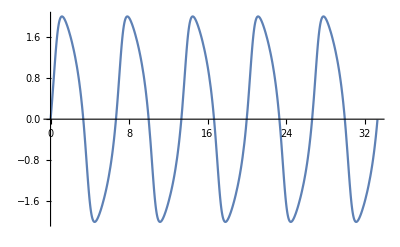

```mathematica
Plot[sol1[t],{t,0,5*periodo}]
```

#### Esta funcion es la misma que se realizo en clase solo que se ha modificado el valor de PE2, se ha transformado PE por Log10[PE + 1] y se regresa este ultimo array.

```mathematica
plotPowerSpectrumLog[f_,t_,n_,tmax_]:=
Module[{w,lw,dt,dw,wnyq,tt,ww,ff,PE,PE2},dt=tmax/n;
dw=2*Pi/tmax;
wnyq=Floor[n/2] dw;
tt=N@Table[t,{t,0,tmax-dt,dt}];
ff=N@Table[f,{t,0,tmax-dt,dt}];
ww=N@Table[w,{w,0,wnyq,dw}];
lw=Length[ww];
PE=Abs[Fourier[ff]];
PE2=Transpose[{ww,Log10[PE[[1;;lw]]+1]}];
Echo[{dw,wnyq}//N];
{GraphicsRow[{Show[{ListPlot[Transpose[{tt,ff}],Filling->Axis],Plot[f[t],{t,0,tmax},PlotStyle->{Thin,Red}]}],ListPlot[PE2,Filling->Axis,PlotRange->All]}],PE2}
]
```

```mathematica
spectrumPlots=plotPowerSpectrumLog[sol1[t],t,200,5*periodo];
```

{0.188591,18.8591}

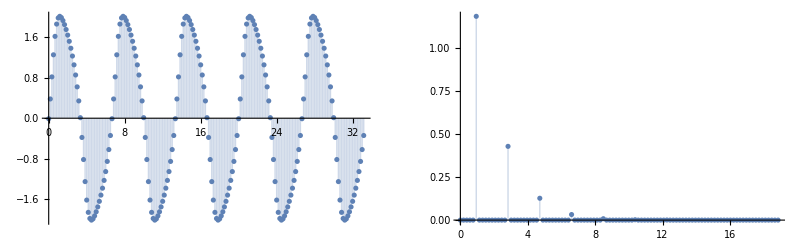

```mathematica
spectrumPlots[[1]]
```

#### Extraemos las frecuencias:

```mathematica
freq1=Cases[spectrumPlots[[2]],{x_,y_}/;y>10^-5->{x,y}]
```

{{0.942956,1.1832},{2.82887,0.428204},{4.71478,0.126884},{6.60069,0.0322943},{8.4866,0.0079504},{10.3725,0.0019706},{12.2584,0.000494699},{14.1443,0.000125488},{16.0302,0.0000317343}}

#### Frecuencias Principales:

```mathematica
Do[Print[Transpose[freq1][[1]][[i]]],{i,1,Length[Transpose[freq1][[1]]]}]
```

0.942956

2.82887

4.71478

6.60069

8.4866

10.3725

12.2584

14.1443

16.0302